## MKP pre 1D rovnicu vedenia tepla

### Integrácia cez kvadratúry, aproximácia integrálu, súčet vážených hodnôt funkcie

```mathematica
(*korene Lagrange polynómu*)
GaussNodesWeights[n_]:=Module[
{x,P,dP,xi,wi},
P=LegendreP[n,x]; (*Legendreho polynóm n-teho stupňa*)
dP=D[P,x];
xi=x/. NSolve[P==0&&-1<x<1,x]; (*nájde všetky korene Pn na (-1,1), gaussove uzly*)
xi=N[xi];
wi=N[2/((1-xi^2) (dP/. x->xi)^2)]; (*váhy*)
Transpose[{xi,wi}] (*zoznam párov xi-uzly, wi-váhy*)
];

(*oddelenie uzlov a váh*)
{xi,wi}=Transpose[GaussNodesWeights[3]]; (*3 bodová*)

(*aproximácia integrálu, číslo*)
GaussQuad[f_,x_,a_,b_]:=
Module[
{
(*musím lineárne presunúť na môj interval, LP len na [-1,1]*)
c=(a+b)/2, (*stred intervalu*)
h=(b-a)/2}, (*1/2 intervalu*)
N@(h*Total[wi*(f/. x->(c+h*xi))]) (*za x dosadím všetky body c + hxi​, ich suma*)
];


GaussQuad[x^4,x,-1,1]
```

0.4

Parametre ulohy

```mathematica
(*−d/dx(a(x)du/dx(x))=f(x)*)
xL=0;xP=1;(*Hranice vypoctovej oblasti*)
a[x_]=(1+x);(*materialova charakteristika*)
f[x_]=-18x^2;(*prava strana*)
α1=1;β1=0;g1=1;(*Paramtre ľavej OP, (n=-1)*)
α2=0;β2=1;g2=0;(*Paramtre pravej OP, (n=+1)*)

(*Pilier, podstavy
b(x) = b(0) + (b(L) - b(0)x)/2
*)

(*A[x_]:=3/4-x/4;             (*prierezová plocha*)
Ey=28*10^9; (*Youngov modul pružnosti*)
rho=2500;(*hustota*)
g=10;(*tiaž*)

a[x_]:=Ey*A[x];
f[x_]:=-rho*g*A[x];        
Q=-5000;                    (*Neumann na x=L*)


*)
```

Presne riesenie

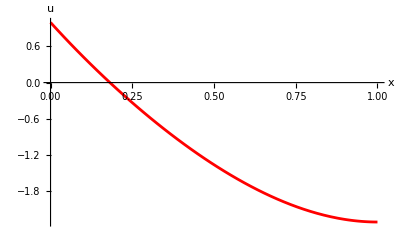

```mathematica
Rovnica=-D[a[x]u'[x],x]==f[x];
riesenie=DSolve[{
Rovnica,
α1 u[xL]+β1 (-a[xL]u'[xL])==g1,
α2 u[xP]+β2 (a[xP]u'[xP])==g2
},u[x],x];
uA[x_]=u[x]/.riesenie[[1]];
plotA=Plot[uA[x], {x,xL,xP},AxesLabel->{Style[x,Large],Style[u,Large]},PlotStyle->Red]
```

MKP, diskretizacia oblasti

```mathematica
s=1;(*stupeň elementu:1=lineárny (2 prvky na elemente),2=kvadratický...*)
NN=4;(*počet elementov, počet rovníc*)
n=s*NN+1;(*počet globálnych uzlov, pre lin = NN +1*)
H=(xP-xL)/NN;(*dĺžka jedného elementu*)
h = H/s;(*vzdialenosť susedných globálnych uzlov*)
```

MKP, zostrojenie aproximacnych funkcii (Lagrangeov tvar)

```mathematica
(*VŠETKY globálne uzly*)
uzly=Table[xL+j*h,{j,0,NN*s}];   (*dĺžka=NN*s+1*)

(*vracia zoznam uzlov patriacich elementu e, (s + 1) po sebe idúcich uzlov*)
uzlyNaElemente[e_]:=uzly[[(e-1)*s+1;;(e-1)*s+s+1]];(*zoznam dĺžky s+1*)

(*vracia globálne indexy uzlov elementu e*)
(*globIdx[2]={3,4,5} -> (U1, U2, U3 na tomto e)*)
globIdx[e_]:=Range[(e-1)*s+1,(e-1)*s+s+1];


(*lokálne aproximačné funkcie*)
(*loc - zoznam uzlov na elemente, množina*)
psiLagrange[x_,loc_,i_]:=
Product[
If[j==i,1, (*kronekerova delta*)
(x-loc[[j]])/(loc[[i]]-loc[[j]])],
{j,1,Length[loc]}
]; (*vráti symbolickú apr.funkciu i-tu*)

(*všetky aproximačné funkcie na všetkých elementoch*)
(*dvojitý zoznam*)
(*{element 1-jeho lok.báza}, {element 2-jeho lok.báza}*)
psiVsetky=
Table[
With[
{loc=uzlyNaElemente[e]},
Table[
psiLagrange[x,loc,i],{i,1,Length[loc]
}
]
],
{e,1,NN}
];

(*derivácie aproximačných funkcií*)
dpsiVsetky=D[psiVsetky,x];


Show[Table[With[{loc=uzlyNaElemente[e],funs=psiVsetky[[e]]},Plot[Evaluate[funs],{x,First[loc],Last[loc]},PlotLegends->None]],{e,1,NN}],PlotRange->All,PlotLabel->"Lagrangeove bázy po elementoch"];

e=2;
loc=uzlyNaElemente[e];

Print["Element e = ",e];
Print["Uzly na elemente (loc) = ",loc];
Print["Globálne indexy uzlov = ",globIdx[e]];
Print["Lokálne Lagrangeove bázy psi_{e,i}(x):"];

Do[Print["  psi_",i,"(x) = ",psiVsetky[[e,i]]],{i,1,Length[loc]}]

Print["\nHodnoty psi_i(loc_j):"];

Do[Print["psi_",i,"(loc_",j,") = ",psiVsetky[[e,i]]/. x->loc[[j]]//N],{i,1,Length[loc]},{j,1,Length[loc]}]
```

Element e = 2

Uzly na elemente (loc) = {1/4,1/2}

Globálne indexy uzlov = {2,3}

Lokálne Lagrangeove bázy psi_{e,i}(x):

psi_1(x) = -4 (-1/2+x)

psi_2(x) = 4 (-1/4+x)

Hodnoty psi_i(loc_j):

psi_1(loc_1) = 1.

psi_1(loc_2) = 0.

psi_2(loc_1) = 0.

psi_2(loc_2) = 1.

MKP, zostrojenie lokalnych matic a pravych stran

```mathematica
(*zintegrujem cez celý element*)
(*pre každý element integrujem dvojicu {Ke,fe}*)
elementMatrices=
Table[
Module[{loc,m,xA,xB,psi,dpsi,Ke,fe},
loc=uzlyNaElemente[e]; (*lokálne uzly na elemente e*)
m=Length[loc]; (*počet uzlových bodov -apr.f. na elemente*)
xA=First[loc];(*začiatok, koniec elementu*)
xB=Last[loc]; 
psi=psiVsetky[[e]]; (*zoznam pre element e*)
dpsi=dpsiVsetky[[e]];

(*Lokálna tuhosť Ke*)
Ke=N@Table[GaussQuad[a[x]*dpsi[[i]]*dpsi[[j]],x,xA,xB],
{i,m},{j,m}
];
(*lokálny vektor fe*)
fe=N@Table[GaussQuad[f[x]*psi[[i]],x,xA,xB],{i,m}];

{Ke,fe}],{e,1,NN}(*zoznam {K1, f1}, {K2, f2}*)
];

(*rozbalenie jedneho elementu*)
{Ke1,fe1}=elementMatrices[[1]];

Print["Ke1 = ",Ke1] 
Print["fe1 = ",fe1]
```

Ke1 = {{4.5,-4.5},{-4.5,4.5}}

fe1 = {-0.0234375,-0.0703125}

MKP, zostrojenie globalnych matic a pravych stran

```mathematica
(*SPOJENIE
- prenesiem lokálne príspevky do globálnych indexov
*)
Clear[K,F,GlobK,GlobF,U];

GlobK=ConstantArray[0.,{n,n}]; (*n-počet globálnych uzlov*)
GlobF=ConstantArray[0.,n];

(* hladám spoločné globálne uzly*)
Do[
Module[
{Ke,fe,g},
{Ke,fe}=elementMatrices[[e]];(* lokálne príspevky elementu e*)
g=globIdx[e]; (*globálne indexy daného elementu e*)
(*Prenesiem Ke Ff DO GLOBÁLU*)
Do[
GlobK[[g[[i]],g[[j]]]]+=Ke[[i,j]], (*ak 2 elementy zdieľajú uzol -> príspevky sa zrátajú*)
{i,Length[g]},
{j,Length[g]}
];
Do[
GlobF[[g[[i]]]]              +=fe[[i]],
{i,Length[g]}
];
],(*zdielané uzly = súčet prvkov viacerých elementov*)
{e,1,NN}
];


GlobK //MatrixForm
GlobF//MatrixForm

(*uloženie „originálu“ pred OP–na reakcie, zložené len z elementov*)
K0=GlobK;F0=GlobF;
```

(4.5 | -4.5 | 0. | 0. | 0.
-4.5 | 10. | -5.5 | 0. | 0.
0. | -5.5 | 12. | -6.5 | 0.
0. | 0. | -6.5 | 14. | -7.5
0. | 0. | 0. | -7.5 | 7.5)

(-0.0234375
-0.328125
-1.17187
-2.57812
-1.89844)

Mechanizmus indexov, čarovanie

```mathematica
(*Globálne indexy*)
Do[
Print["e = ",e," | g = ",globIdx[e]];,{e,1,NN}
]

e=2;
{Ke,fe}=elementMatrices[[e]];
g=globIdx[e];

Print["Element e = ",e];
Print["Globálne indexy g = ",g];
Print["Lokálna matica Ke:"];
Print[MatrixForm[Ke]];
Print["Lokálny vektor fe:"];
Print[fe];
Do[
Print[
"Lokálne (i,j)=(",i,",",j,")  ->  Globálne (",g[[i]],",",g[[j]]")  |  pripočítavam Ke[[",i,",",j,"]] = ",Ke[[i,j]]],
{i,Length[g]},
{j,Length[g]}
]
```

e = 1 | g = {1,2}

e = 2 | g = {2,3}

e = 3 | g = {3,4}

e = 4 | g = {4,5}

Element e = 2

Globálne indexy g = {2,3}

Lokálna matica Ke:

(5.5 | -5.5
-5.5 | 5.5)

Lokálny vektor fe:

{-0.257812,-0.398437}

Lokálne (i,j)=(1,1)  ->  Globálne (2,2 )  |  pripočítavam Ke[[1,1]] = 5.5

Lokálne (i,j)=(1,2)  ->  Globálne (2,3 )  |  pripočítavam Ke[[1,2]] = -5.5

Lokálne (i,j)=(2,1)  ->  Globálne (3,2 )  |  pripočítavam Ke[[2,1]] = -5.5

Lokálne (i,j)=(2,2)  ->  Globálne (3,3 )  |  pripočítavam Ke[[2,2]] = 5.5

MKP, zahrnutie okrajovych podmienok

```mathematica
(*OP----------------------------------------------------
- dirichlet prepisuje
- Neumann pripočíta
*)
(*ĽAVÝ OKRAJ–Dirichlet u(0)=g1/α1=0, na prvo uzle, predpisujem U[1] = val*)
If[
α1!=0,
val=g1/α1;
(*U1 je známe (Dirichlet),preto členy K(..,1)*U1 presúvam z ľavej strany do PS*)
GlobF=GlobF-GlobK[[All,1]]*val; 
GlobK[[1,All]]=0; 
GlobK[[All,1]]=0; 
GlobK[[1,1]]=1; (*koeficient pri 1.U1 = val*)
GlobF[[1]]=val;
];

(*ĽAVÝ OKRAJ–NEUMANN - MÍNUS, vonkajšia normála n = -1*)
If[
β1!=0,
GlobK[[1,1]]+=α1/β1;
GlobF[[1]]-=g1/β1;
];


(*PRAVÝ OKRAJ Dirichlet u(L)=g2/α2, na poslednom uzle n*)
If[α2!=0,
val=g2/α2;
GlobF=GlobF-GlobK[[All,n]]*val;
GlobK[[n,All]]=0;
GlobK[[All,n]]=0;
GlobK[[n,n]]=1;
GlobF[[n]]=val;
];

(*PRAVÝ OKRAJ NEUMANN, PLUS*)
If[
β2!=0,
GlobK[[n,n]]+=α2/β2;
GlobF[[n]]+=g2/β2;
];
```

```mathematica
MatrixForm[GlobK]
GlobF//MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 10. | -5.5 | 0. | 0.
0 | -5.5 | 12. | -6.5 | 0.
0 | 0. | -6.5 | 14. | -7.5
0 | 0. | 0. | -7.5 | 7.5)

(1
4.17187
-1.17187
-2.57812
-1.89844)

MKP, riesenie rovnic, konstrukcia priblizneho riesenia, zobrazenie presneho aj priblizneho riesenia

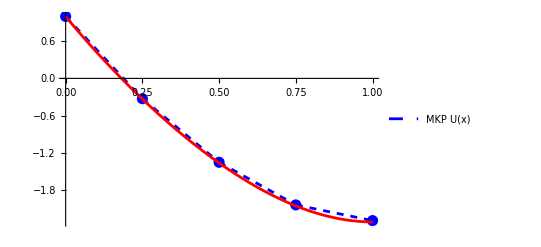

U1 = 1.  Un = -2.29694

Dlžka[uzly] = 5

Dĺžka[U] = 5

```mathematica
(* výpočet vektora uzlových hodnôt U1,U1,...,aproximácie rešenie v glob.uzl.bodoch*)
U=LinearSolve[N@GlobK,N@GlobF] ;

Clear[uMKP]
(*rekonštrukcia*)
uMKP[x_]:=Piecewise@Table[
With[
{
loc=uzlyNaElemente[e],(*uzly elementu*)
idx=globIdx[e]}                  (*globálne indexy tých uzlov*),
{
(*zosumujem skalárny súčin U.psi*)
U[[idx]].psiVsetky[[e]],(*psiVsetky -> vektor aproximacnych funkcii*)
loc[[1]]<=x<=loc[[-1]]  (*teda x leží v intervale elementu e*)
}
],{e,1,NN}
];
plotU=Plot[uMKP[x],{x,xL,xP},PlotStyle->{Blue,Dashed},PlotLegends->{"MKP U(x)"},PlotRange->All]; (*súvislá MKP aproximácia*)

plotPts=ListPlot[Transpose[{uzly,U}],PlotStyle->{Blue,PointSize[0.02]}];(*uzlvé hodnoty, hodnoty v uzloch, vypočítané, uzly rozdelené*)

Show[plotU,plotPts, plotA]
Print["U1 = ",U[[1]],"  Un = ",U[[n]]];
Print["Dlžka[uzly] = ",Length[uzly]];
Print["Dĺžka[U] = ",Length[U]];
```

MKP, vypocet chyb a EOC (m=1,2,4,8,16,32)

Vo vseobecnosti ma MKP v L2-chybe presnost radu
	p = (stupen elementov) + 1 (cize s+1)

a v Energetickej chybe radu
	p = (stupen elementov) - (rad rovnice)/2 + 1 (cize s u nas)

-Graphics-

-Graphics-

```mathematica
(*pred výpočtami si pripravím prázdne polia na chyby*)
L2pole={};
ENpole={};
sPole = {};
NPole = {};
EOCL2pole = {};
EOCENpole = {};
```

### Chyby

```mathematica
(*L2 chyba aproximácia - analytické riešenie*)
(*„Priemerná“chyba v hodnote funkcie*)
L2=Sqrt@NIntegrate[(uMKP[x]-uA[x])^2,{x,xL,xP}]
uMKPder[x_]:=D[uMKP[x],x];
duA[x_]:= D[uA[x],x];

energetickaChyba=Sqrt@NIntegrate[a[x] (uMKPder[x]-duA[x])^2,{x,xL,xP}]

L2pole=Append[L2pole,L2];
ENpole=Append[ENpole,energetickaChyba];
sPole = Append[sPole, s];
NPole = Append[NPole, NN];


EOCL2=Log[L2pole[[1]]/L2pole[[2]]]/Log[2]
EOCEN=Log[ENpole[[1]]/ENpole[[2]]]/Log[2]
EOCL2pole = Append[EOCL2pole,EOCL2] ;
EOCENpole = Append[EOCENpole,EOCEN] ;
```

0.0455456

0.557792

1.97438

0.971449

```mathematica
tabulkaData=Table[
{sPole[[i]],
NPole[[i]],
L2pole[[i]],
If[i==1,"-",EOCL2pole[[i]]],
ENpole[[i]],
If[i==1,"-",EOCENpole[[i]]]
},
{i,1,Length[sPole]}
];
Grid[
Prepend[
tabulkaData,
{"s","N","L2 chyba","EOC L2","EN chyba","EOC EN"}
],
Frame->All,
Alignment->Center, 
Background->{{{None,Yellow}},{{LightPurple,None}}}
]
```

s | N | L2 chyba | EOC L2 | EN chyba | EOC EN
1 | 2 | 0.178975 | - | 1.09372 | -
1 | 4 | 0.0455456 | 1.97438 | 0.557792 | 0.971449

### Q - čka

-Graphics-

```mathematica
(*Dopočítanie Q-čok, sekundárne neznáme, q(x)=a(x)du/dx(x)*)
Odpočet=K0.U-F0;   (*čistá tuhosť, pred OP, čistá PS*)
Q11=Odpočet[[1]]  (*Q naľavo*)
Q2N = Odpočet[[-1]] (*Q napravo*)
```

6.

-4.44089×10^-16